```mathematica
r=8;
np=5;
p=Table[{1+1.0r Cos[i],4.0+r Sin[i]},{i,0,Pi/6,Pi/(6*np)}]

k=Table[{i},{i,0,Pi/6,Pi/(6*np)}]
```

{{9.,4.},{8.95618,4.83623},{8.82518,5.66329},{8.60845,6.47214},{8.30836,7.25389},{7.9282,8.}}

{{0},{π/30},{π/15},{π/10},{(2 π)/15},{π/6}}

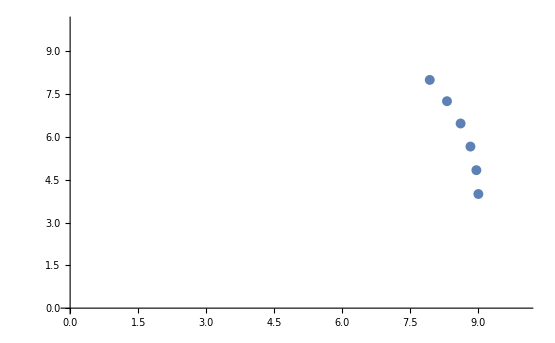

```mathematica
ListPlot[p,PlotRange->{{0,10},{0,10}}]
```

```mathematica
PuntosAf1={{Pi/30,3740.83},{Pi/15,4053.44} ,{Pi/10,4639.15},{2Pi/15,5087.16},{Pi/6,5443.42}};
PuntosAf2={{Pi/30,3385.2},{Pi/15,3443.99}, {Pi/10,3137.43},{2Pi/15,2736.31},{Pi/6,2277.94}};


PuntosBf1={{Pi/30,2306.38},{Pi/15,2473.6} ,{Pi/10,2816.28},{2Pi/15,3124.98},{Pi/6,3405.01}};
PuntosBf2={{Pi/30,2192.7},{Pi/15,2484.48}, {Pi/10,2181.23},{2Pi/15,1943.31},{Pi/6,1598.05}};

PuntosCf1={{Pi/30,2305.43},{Pi/15,2377.77} ,{Pi/10,2589.86},{2Pi/15,3233.03},{Pi/6,3465.87}};
PuntosCf2={{Pi/30,2284.15},{Pi/15,2666.88}, {Pi/10,2925.59},{2Pi/15,1447.46},{Pi/6,1915.36}};
```

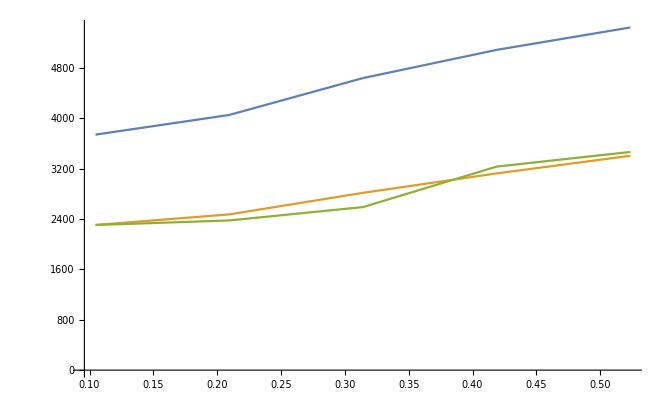

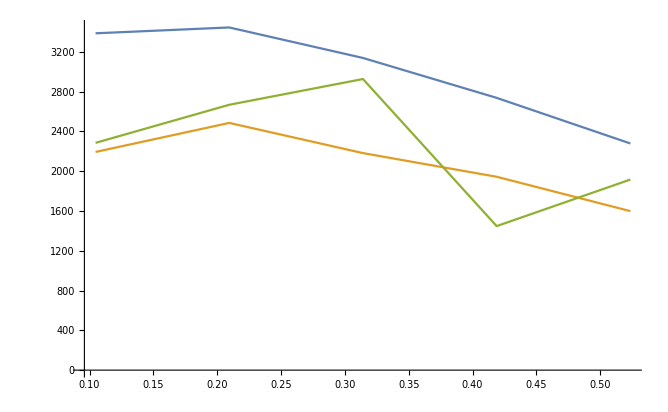

```mathematica
ListPlot[{PuntosAf1,PuntosBf1,PuntosCf1},Joined->True]
ListPlot[{PuntosAf2,PuntosBf2,PuntosCf2},Joined->True]
```